```mathematica
Quit
```

The notebook illustrates how to use the package AnalyticSpinOrbitsHamiltonJacobi , which provides the analytic spin corrections to nearly equatorial periodic and homoclinic orbits  See arXiv: 2510.09597 (https://arxiv.org/abs/2510.09597 )

PREREQUISITEs: the following packages are needed
-  SpinOrbitsHamiltonJacobi from the repo https://github.com/gabriel-andres-piovano/Spinning-Body-Hamilton-Jacobi. It computes the spin-corrections for generic orbits numerically, and is used for sanity checks.
- KerrGeodesics from the BPToolkit. This package is needed to calculate the location of the geodesic separatrix.

If you make use of this notebook, please acknowledge 
- “Piovano, Pantelidou, Mac Uilliam and Witzany” PRD 111, 044009 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.111.044009 ). The code is available at https://github.com/gabriel-andres-piovano/Spinning-Body-Hamilton-Jacobi
- “Piovano” arXiv:2510.09597 (https://arxiv.org/abs/2510.09597 )
- KerrGeodesics package,  (https://zenodo.org/records/8108265 ) of the  BHPToolkit

IMPORTANT NOTE: the code of https://github.com/gabriel-andres-piovano/Spinning-Body-Hamilton-Jacobi (see the Mathematica notebook “Corrections_orbits.nb’’  within) is in perfect agreement with the results of  PRD 108, 044041 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.108.044041 ). However, their code is NOT publicly available. Thus, this notebook only compare with the results of the Hamilton-Jacobi formalism.

### Convention for EoM

Here we follow the same convention of  CQG, Volume 37, Number 14  (https://iopscience.iop.org/article/10.1088/1361-6382/ab79d5 )

r_1== p/(1-e)
r_2== p/(1+e)
z_1==√(1-x^2)

or

p==2(r_1 r_2)/(r_1+r_2)
e== (r_1-r_2)/(r_1+r_2)
x ==  Sign[ℒ]√(1-z_1^2)

(circular) 0<e<1 (parabolic)
(retrograde) -1 < x < 1 (prograde)
p> p_LSO(e,x)

Equatorial orbits

x==±1
z_1==0
𝒬 ==0

“spar” and “sort” are the parallel and orthogonal component of the spin to the total angular momentum.

### Loading all the necessary files

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<KerrGeodesics`
```

```mathematica
Get["AnalyticSpinOrbitsHamiltonJacobi.wl"]
```

```mathematica
Get["SpinOrbitsHamiltonJacobi.wl"]
```

## Periodic orbits, fixed turning points

### Calculation orbits

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

```mathematica
AbsoluteTiming[corrFTGeneric=KerrSpinOrbitCorrectionDHPar[0.9,12,0.2,0.999995,8,8];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{2.92264,Null}

```mathematica
AbsoluteTiming[corrFT=KerrNearEqSpinOrbitCorrFTPer[0.9,12,0.2,1];]
```

{0.003741,Null}

```mathematica
AbsoluteTiming[corrFTFourier=KerrNearEqSpinOrbitCorrFTPerFourier[0.9,12,0.2,1,8];]
```

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.020761,Null}

### Constants of motion and frequencies

```mathematica
{corrFTGeneric["Eg"],corrFTGeneric["Lzg"]}
```

{0.961473,3.74739}

```mathematica
{corrFT["Eg"],corrFT["Lzg"]}
```

{0.961473,3.74741}

```mathematica
{corrFTFourier["Eg"],corrFTFourier["Lzg"]}
```

{0.961473,3.74741}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFTGeneric["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.75557,3.89443}

```mathematica
corrFT["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.75557,3.89443}

```mathematica
corrFTFourier["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.75557,3.89443}

BL frequencies. Order of appearance:  Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFTGeneric["BLFrequenciesGeo"]
```

{0.0181042,0.0215567,0.0223538}

```mathematica
corrFT["BLFrequenciesGeo"]
```

{0.0181042,0.0215567,0.0223538}

```mathematica
corrFTFourier["BLFrequenciesGeo"]
```

{0.0181042,0.0215567,0.0223538}

### Oscillating terms geodesic coordinate time and azimuthal trajectories

```mathematica
{corrFTGeneric[ "Δtrg"][23π/5],corrFTGeneric[ "Δϕrg"][23π/5]}
```

{-19.9583+2.36686×10^-16 ⅈ,0.00899143}

```mathematica
{corrFT[ "Δtrg"][23π/5],corrFT[ "Δϕrg"][23π/5]}
```

{-19.9583,0.00899142}

```mathematica
{corrFTFourier[ "Δtrg"][23π/5],corrFTFourier[ "Δϕrg"][23π/5]}
```

{-19.9583,0.00899142}

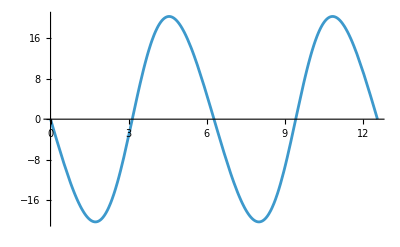

```mathematica
Plot[corrFTFourier[ "Δtrg"][wr],{wr,0,4π}]
```

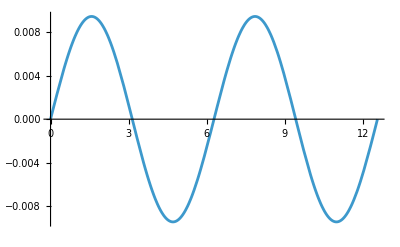

```mathematica
Plot[corrFTFourier[ "Δϕrg"][wr],{wr,0,4π}]
```

### Shifts constants of motion

```mathematica
{corrFTGeneric["Es"],corrFTGeneric["Jzs"]}
```

{-0.000903329,0.848971}

```mathematica
{corrFT["Es"],corrFT["Jzs"]}
```

{-0.000903328,0.848979}

```mathematica
{corrFTFourier["Es"],corrFTFourier["Jzs"]}
```

{-0.000903328,0.848979}

### Shifts frequencies

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFTGeneric["MinoFrequenciesCorrection"]
```

{-0.245437,0.12346,-0.0459382,-0.113893}

```mathematica
corrFT["MinoFrequenciesCorrection"]
```

{-0.245437,0.123459,-0.113892}

```mathematica
corrFTFourier["MinoFrequenciesCorrection"]
```

{-0.245437,0.123459,-0.113892}

BL frequencies. Order of appearance: Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFTGeneric["BLFrequenciesCorrection"]
```

{0.000734155,-0.000233313,-0.000622246}

```mathematica
corrFT["BLFrequenciesCorrection"]
```

{0.000734155,-0.000622244}

```mathematica
corrFTFourier["BLFrequenciesCorrection"]
```

{0.000734155,-0.000622244}

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

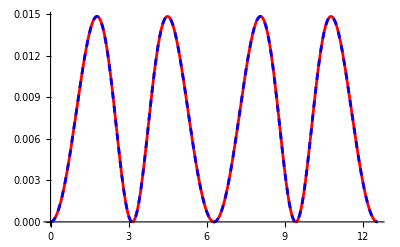

```mathematica
Show[Plot[corrFT["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFTGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrFTFourier["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFTGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the radial velocities

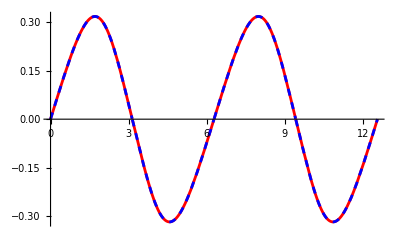

```mathematica
Show[Plot[corrFT["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFTGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrFTFourier["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFTGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

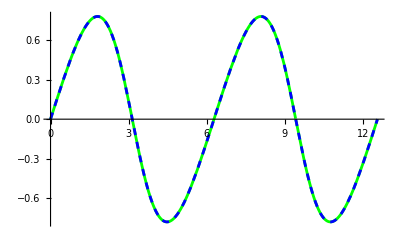

```mathematica
Show[Plot[corrFT["Δδtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFTGeneric["Δδtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrFTGeneric["Δδtpar"][wr,0]//Simplify
```

(0.768052-2.34229×10^-17 ⅈ) Sin[wr]-(0.18047-9.36914×10^-17 ⅈ) Cos[wr] Sin[wr]+(0.0117226-1.83709×10^-18 ⅈ) Sin[3 wr]-(0.00151905-1.65338×10^-17 ⅈ) Sin[4 wr]+0.000192939 Sin[5 wr]-(0.0000240347+2.2045×10^-17 ⅈ) Sin[6 wr]+(2.94526×10^-6+4.72394×10^-18 ⅈ) Sin[7 wr]-(3.56063×10^-7+4.4081×10^-39 ⅈ) Sin[8 wr]

```mathematica
corrFTFourier["Δδtpar"][wr]//Simplify//N
```

Re[((0.768051-1.67731×10^-15 ⅈ)-(0.18047-1.05703×10^-15 ⅈ) Cos[wr]) Sin[wr]+(0.0117225-3.12304×10^-17 ⅈ) Sin[3. wr]-(0.00151905+1.14096×10^-16 ⅈ) Sin[4. wr]+(0.000192939-1.60812×10^-16 ⅈ) Sin[5. wr]-(0.0000240346-1.23702×10^-16 ⅈ) Sin[6. wr]+(2.94525×10^-6+2.32666×10^-17 ⅈ) Sin[7. wr]-(3.56061×10^-7+5.28673×10^-17 ⅈ) Sin[8. wr]]

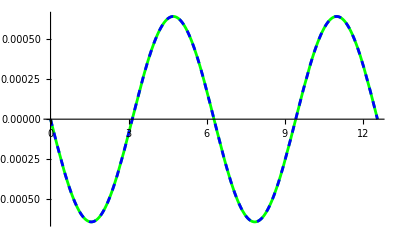

```mathematica
Show[Plot[corrFT["Δδϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFTGeneric["Δδϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrFTGeneric["Δδϕpar"][wr,0]//Simplify//N
```

-0.000643772 Sin[wr]-2.22678×10^-6 Cos[wr] Sin[wr]-5.38363×10^-7 Sin[3. wr]-2.16449×10^-10 Sin[4. wr]+2.51968×10^-13 Sin[5. wr]-1.0509×10^-14 Sin[6. wr]+7.09919×10^-17 Sin[7. wr]+8.83164×10^-17 Sin[8. wr]

```mathematica
corrFTFourier["Δδϕpar"][wr]//Simplify//N
```

Re[(-0.000643766-2.22529×10^-6 Cos[wr]) Sin[wr]-5.38344×10^-7 Sin[3. wr]-2.16501×10^-10 Sin[4. wr]+2.50865×10^-13 Sin[5. wr]-1.04806×10^-14 Sin[6. wr]-4.23456×10^-17 Sin[7. wr]-(6.88906×10^-19-3.44453×10^-19 ⅈ) Sin[8. wr]]

#### Spin corrections to the coordinate time and azimuthal velocities

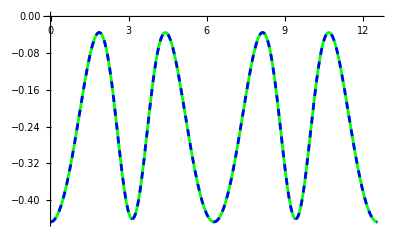

```mathematica
Show[Plot[corrFT["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFTGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

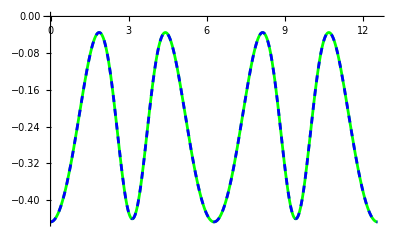

```mathematica
Show[Plot[corrFTFourier["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFTGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

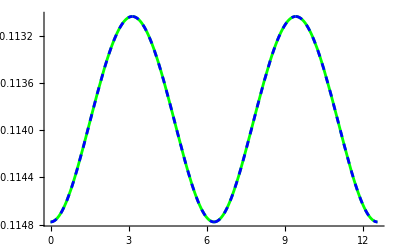

```mathematica
Show[Plot[corrFT["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFTGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

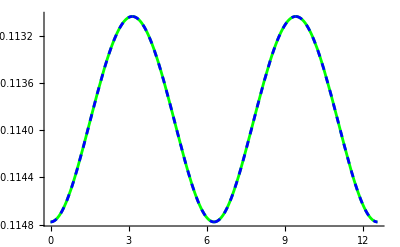

```mathematica
Show[Plot[corrFTFourier["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFTGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrFT["MinoPrecessionFrequency"]
```

3.46735

Precession phase

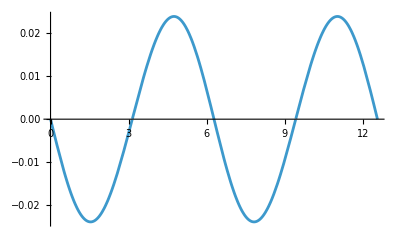

```mathematica
Plot[corrFT["ψp"][wr],{wr,0,4π}]
```

Spin correction to the polar motion

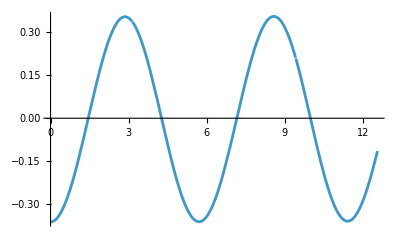

```mathematica
Plot[corrFT["δzort"][wr],{wr,0,4π}]
```

## Periodic orbits, fixed constants of motion

### Calculation orbits

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

```mathematica
AbsoluteTiming[corrFCGeneric=KerrSpinOrbitCorrectionFCPar[0.9,12,0.2,0.9999995`45,8,8];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{2.85354,Null}

```mathematica
AbsoluteTiming[corrFC=KerrNearEqSpinOrbitCorrFCPer[0.9,12,0.2,1];]
```

{0.003908,Null}

```mathematica
AbsoluteTiming[corrFCFourier=KerrNearEqSpinOrbitCorrFCPerFourier[0.9,12,0.2,1,8];]
```

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.020314,Null}

### Constants of motion and frequencies

```mathematica
{corrFCGeneric["Eg"],corrFCGeneric["Lzg"]}
```

{0.961473,3.74741}

```mathematica
{corrFC["Eg"],corrFC["Lzg"]}
```

{0.961473,3.74741}

```mathematica
{corrFCFourier["Eg"],corrFCFourier["Lzg"]}
```

{0.961473,3.74741}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFCGeneric["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.75557,3.89443}

```mathematica
corrFC["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.75557,3.89443}

```mathematica
corrFCFourier["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.75557,3.89443}

BL frequencies. Order of appearance: Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFCGeneric["BLFrequenciesGeo"]
```

{0.0181042,0.0215567,0.0223538}

```mathematica
corrFC["BLFrequenciesGeo"]
```

{0.0181042,0.0215567,0.0223538}

```mathematica
corrFCFourier["BLFrequenciesGeo"]
```

{0.0181042,0.0215567,0.0223538}

### Oscillating terms geodesic coordinate time and azimuthal trajectories

```mathematica
{corrFCGeneric[ "Δtrg"][23π/5],corrFCGeneric[ "Δϕrg"][23π/5]}
```

{-19.9583-3.37137×10^-15 ⅈ,0.00899142}

```mathematica
{corrFC[ "Δtrg"][23π/5],corrFC[ "Δϕrg"][23π/5]}
```

{-19.9583,0.00899142}

```mathematica
{corrFCFourier[ "Δtrg"][23π/5],corrFCFourier[ "Δϕrg"][23π/5]}
```

{-19.9583,0.00899142}

```mathematica
Plot[corrFTFourier[ "Δtrg"][wr],{wr,0,4π}]
```

-Graphics-

```mathematica
Plot[corrFTFourier[ "Δϕrg"][wr],{wr,0,4π}]
```

-Graphics-

### Shifts frequencies

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFCGeneric["MinoFrequenciesCorrection"]
```

{-47.6353,-0.870534,-0.89326,-0.870391}

```mathematica
corrFC["MinoFrequenciesCorrection"]
```

{-47.6353,-0.870534,-0.87039}

```mathematica
corrFCFourier["MinoFrequenciesCorrection"]
```

{-47.6353,-0.870534,-0.87039}

BL frequencies. Order of appearance:  Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFCGeneric["BLFrequenciesCorrection"]
```

{-0.0000466881,0.000766868,0.00111607}

```mathematica
corrFC["BLFrequenciesCorrection"]
```

{-0.0000466881,0.00111607}

```mathematica
corrFCFourier["BLFrequenciesCorrection"]
```

{-0.0000466881,0.00111607}

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

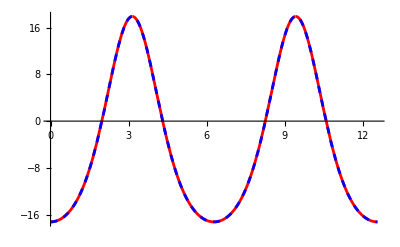

```mathematica
Show[Plot[corrFC["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFCGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrFCFourier["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFCGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the radial velocities

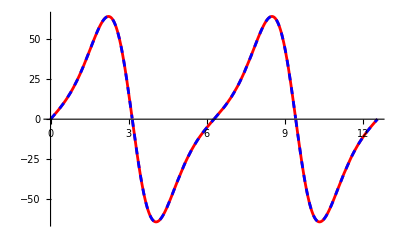

```mathematica
Show[Plot[corrFC["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFCGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrFCFourier["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFCGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

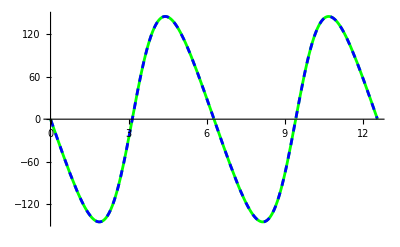

```mathematica
Show[Plot[corrFC["Δδtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["Δδtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrFCGeneric["Δδtpar"][wr,0]//Simplify//N
```

(-141.26-5.10117×10^-14 ⅈ) Sin[wr]+(43.7672+1.52933×10^-14 ⅈ) Cos[wr] Sin[wr]-(3.07619+7.51735×10^-16 ⅈ) Sin[3. wr]+(0.408892-6.34564×10^-15 ⅈ) Sin[4. wr]-(0.0524079-1.2324×10^-15 ⅈ) Sin[5. wr]+(0.0065473+2.44812×10^-15 ⅈ) Sin[6. wr]-(0.000802557+6.21492×10^-15 ⅈ) Sin[7. wr]+(0.0000969442-3.38693×10^-16 ⅈ) Sin[8. wr]

```mathematica
corrFCFourier["Δδtpar"][wr]//Simplify//N
```

Re[((-141.26-3.95938×10^-14 ⅈ)+(43.7672+1.4012×10^-14 ⅈ) Cos[wr]) Sin[wr]-(3.07619-3.88097×10^-15 ⅈ) Sin[3. wr]+(0.408892-1.08274×10^-15 ⅈ) Sin[4. wr]-(0.0524079-1.32835×10^-15 ⅈ) Sin[5. wr]+(0.0065473-4.661×10^-15 ⅈ) Sin[6. wr]-(0.000802556+1.8838×10^-15 ⅈ) Sin[7. wr]+(0.0000969441+6.5691×10^-15 ⅈ) Sin[8. wr]]

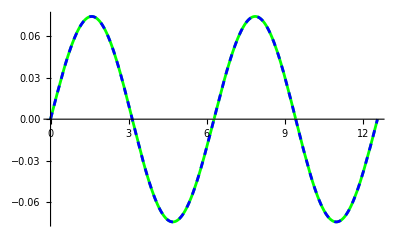

```mathematica
Show[Plot[corrFC["Δδϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["Δδϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrFCGeneric["Δδϕpar"][wr,0]//Simplify//N
```

0.0745298 Sin[wr]-0.000839241 Cos[wr] Sin[wr]-2.39121×10^-6 Sin[3. wr]-2.22347×10^-10 Sin[4. wr]-1.42041×10^-11 Sin[5. wr]-1.1924×10^-13 Sin[6. wr]-1.15901×10^-16 Sin[7. wr]

```mathematica
corrFCFourier["Δδϕpar"][wr]//Simplify//N
```

Re[(0.0745298-0.000839241 Cos[wr]) Sin[wr]-2.39121×10^-6 Sin[3. wr]-2.2236×10^-10 Sin[4. wr]-1.42041×10^-11 Sin[5. wr]-1.19227×10^-13 Sin[6. wr]-1.14874×10^-16 Sin[7. wr]+(4.8576×10^-18-2.4288×10^-18 ⅈ) Sin[8. wr]]

#### Spin corrections to the coordinate time and azimuthal velocities

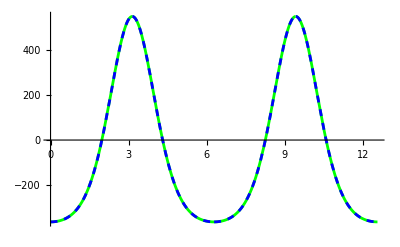

```mathematica
Show[Plot[corrFC["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

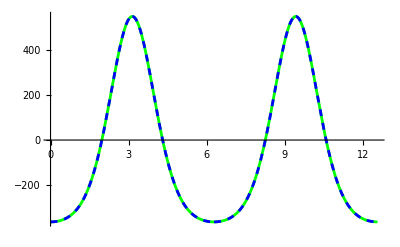

```mathematica
Show[Plot[corrFCFourier["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

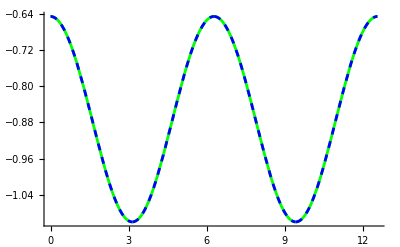

```mathematica
Show[Plot[corrFC["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

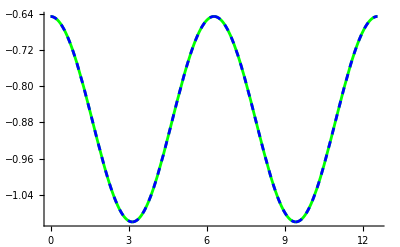

```mathematica
Show[Plot[corrFCFourier["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrFC["MinoPrecessionFrequency"]
```

3.46735

Precession phase

```mathematica
Plot[corrFC["ψp"][wr],{wr,0,4π}]
```

-Graphics-

Spin correction to the polar motion

```mathematica
Plot[corrFC["δzort"][wr],{wr,0,4π}]
```

-Graphics-

## Periodic orbits, fixed eccentricity

### Calculation orbits

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

```mathematica
AbsoluteTiming[corrFEGeneric=KerrSpinOrbitCorrectionFEParEq[0.9,12,0.2,1,8];]
```

Calculating ξ_r Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.027291,Null}

```mathematica
AbsoluteTiming[corrFE=KerrNearEqSpinOrbitCorrFEPer[0.9,12,0.2,1];]
```

{0.007022,Null}

```mathematica
AbsoluteTiming[corrFEFourier=KerrNearEqSpinOrbitCorrFEPerFourier[0.9,12,0.2,1,8];]
```

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.025014,Null}

### Constants of motion and frequencies

```mathematica
{corrFEGeneric["Eg"],corrFEGeneric["Lzg"]}
```

{0.961473,3.74741}

```mathematica
{corrFE["Eg"],corrFE["Lzg"]}
```

{0.961473,3.74741}

```mathematica
{corrFEFourier["Eg"],corrFEFourier["Lzg"]}
```

{0.961473,3.74741}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFEGeneric["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.89443}

```mathematica
corrFE["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.75557,3.89443}

```mathematica
corrFEFourier["MinoFrequenciesGeo"]
```

{174.218,3.15408,3.75557,3.89443}

BL frequencies. Order of appearance: Ω_t , Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFEGeneric["BLFrequenciesGeo"]
```

{0.0181042,0.0223538}

```mathematica
corrFE["BLFrequenciesGeo"]
```

{0.0181042,0.0215567,0.0223538}

```mathematica
corrFEFourier["BLFrequenciesGeo"]
```

{0.0181042,0.0215567,0.0223538}

### Oscillating terms geodesic coordinate time and azimuthal trajectories

```mathematica
{corrFEGeneric[ "Δtrg"][23π/5],corrFEGeneric[ "Δϕrg"][23π/5]}
```

{18.1616+2.50698×10^-15 ⅈ,-0.00895825}

```mathematica
{corrFE[ "Δtrg"][23π/5],corrFE[ "Δϕrg"][23π/5]}
```

{18.1616,-0.00895825}

```mathematica
{corrFEFourier[ "Δtrg"][23π/5],corrFEFourier[ "Δϕrg"][23π/5]}
```

{18.1616,-0.00895825}

```mathematica
Plot[corrFTFourier[ "Δtrg"][wr],{wr,0,4π}]
```

-Graphics-

```mathematica
Plot[corrFTFourier[ "Δϕrg"][wr],{wr,0,4π}]
```

-Graphics-

### Shifts constants of motion

```mathematica
{corrFEGeneric["Es"],corrFEGeneric["Jzs"]}
```

{-0.00031744,0.874787}

```mathematica
{corrFE["Es"],corrFE["Jzs"]}
```

{-0.00031744,0.874787}

```mathematica
{corrFEFourier["Es"],corrFEFourier["Jzs"]}
```

{-0.00031744,0.874787}

### Shifts frequencies

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFEGeneric["MinoFrequenciesCorrection"]
```

{4.84882,0.152786,-0.0905052}

```mathematica
corrFE["MinoFrequenciesCorrection"]
```

{4.84882,0.152786,-0.0905052}

```mathematica
corrFEFourier["MinoFrequenciesCorrection"]
```

{4.84882,0.152786,-0.0905052}

BL frequencies. Order of appearance:  Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFEGeneric["BLFrequenciesCorrection"]
```

{0.000373109,-0.00114164}

```mathematica
corrFE["BLFrequenciesCorrection"]
```

{0.000373109,-0.00114164}

```mathematica
corrFEFourier["BLFrequenciesCorrection"]
```

{0.000373109,-0.00114164}

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

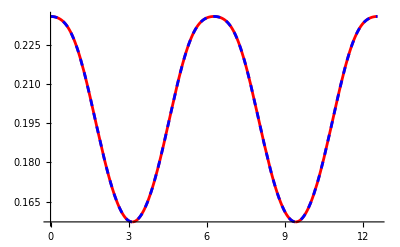

```mathematica
Show[Plot[corrFEFourier["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFEGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the radial velocities

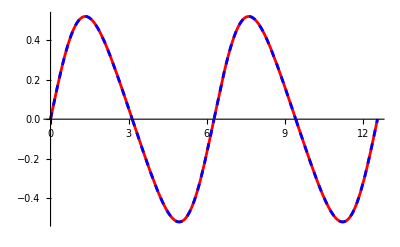

```mathematica
Show[Plot[corrFE["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFEGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrFEFourier["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFEGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

```mathematica
corrFEGeneric["Δδtpar"][wr,0]//Simplify//N
```

(-0.332439-3.68649×10^-17 ⅈ) Sin[wr]-(0.114601+1.09126×10^-16 ⅈ) Cos[wr] Sin[wr]-(0.00874424+9.09387×10^-18 ⅈ) Sin[3. wr]-(0.00123444+1.15487×10^-17 ⅈ) Sin[4. wr]-(0.0001651-1.6369×10^-17 ⅈ) Sin[5. wr]-(0.0000212814+7.04244×10^-18 ⅈ) Sin[6. wr]-(2.67156×10^-6-3.39344×10^-18 ⅈ) Sin[7. wr]-(3.28804×10^-7-1.36408×10^-17 ⅈ) Sin[8. wr]

```mathematica
corrFEFourier["Δδtpar"][wr]//Simplify//N
```

Re[((-0.332439+3.91649×10^-15 ⅈ)-(0.114601-8.28064×10^-16 ⅈ) Cos[wr]) Sin[wr]-(0.00874424-5.54388×10^-17 ⅈ) Sin[3. wr]-(0.00123444-2.32649×10^-16 ⅈ) Sin[4. wr]-(0.0001651-1.87087×10^-16 ⅈ) Sin[5. wr]-(0.0000212814+6.13085×10^-17 ⅈ) Sin[6. wr]-(2.67156×10^-6+6.19773×10^-17 ⅈ) Sin[7. wr]-(3.28804×10^-7-1.36408×10^-17 ⅈ) Sin[8. wr]]

```mathematica
corrFEGeneric["Δδϕpar"][wr,0]//Simplify//N
```

0.000898931 Sin[wr]-8.99935×10^-7 Cos[wr] Sin[wr]+5.34975×10^-7 Sin[3. wr]-2.17901×10^-10 Sin[4. wr]-2.82493×10^-13 Sin[5. wr]-1.02223×10^-14 Sin[6. wr]+3.85624×10^-17 Sin[7. wr]-8.5255×10^-19 Sin[8. wr]

```mathematica
corrFEFourier["Δδϕpar"][wr]//Simplify//N
```

Re[(0.000898931-8.99935×10^-7 Cos[wr]) Sin[wr]+5.34975×10^-7 Sin[3. wr]-2.17901×10^-10 Sin[4. wr]-2.82506×10^-13 Sin[5. wr]-1.02277×10^-14 Sin[6. wr]+3.86409×10^-17 Sin[7. wr]-8.5255×10^-19 Sin[8. wr]]

#### Spin corrections to the coordinate time and azimuthal velocities

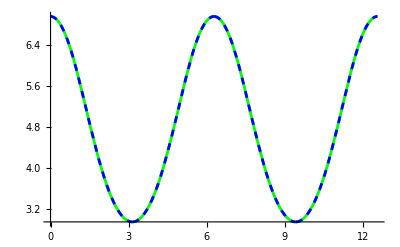

```mathematica
Show[Plot[corrFE["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFEGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

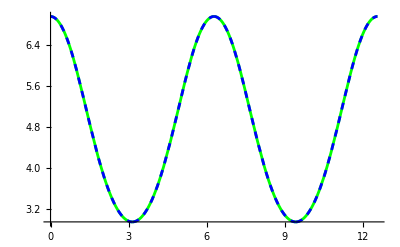

```mathematica
Show[Plot[corrFEFourier["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFEGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

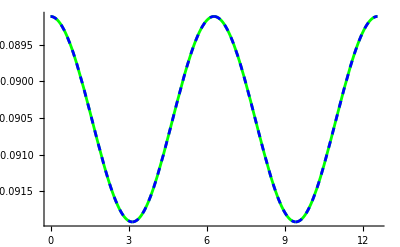

```mathematica
Show[Plot[corrFE["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFEGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

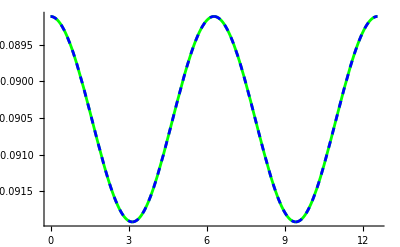

```mathematica
Show[Plot[corrFEFourier["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFEGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrFE["MinoPrecessionFrequency"]
```

3.46735

Precession phase

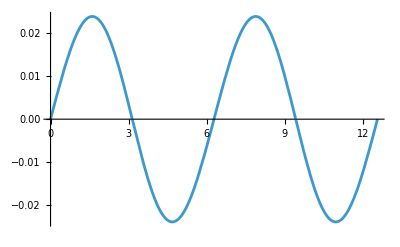

```mathematica
Plot[corrFE["ψp"][wr],{wr,0,4π}]
```

Spin correction to the polar motion

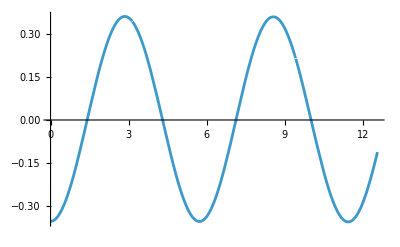

```mathematica
Plot[corrFE["δzort"][wr],{wr,0,4π}]
```

## Homoclinic orbits

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aHom=0.9`55;
eccHom=0.45`55;
```

```mathematica
psepgeo=KerrGeoSeparatrix[aHom,eccHom,1]
```

2.7743315642164893578740640805413320785590353773155034

```mathematica
r1geo=psepgeo/(1-eccHom);
r2geo=psepgeo/(1+eccHom);
```

In this Section, we also checked that the shifts to periodic orbits converge to the homoclinic orbits near the separatrix.

### Calculation orbits

```mathematica
AbsoluteTiming[corrFEHom=KerrNearEqSpinOrbitCorrFEHom[aHom,psepgeo,eccHom,1];]
```

{0.008229,Null}

```mathematica
AbsoluteTiming[corrFENearHom=KerrNearEqSpinOrbitCorrFEPer[aHom,psepgeo+10^(-13),eccHom,1];]
```

{0.012112,Null}

### Constants of motion and frequencies

```mathematica
{corrFEHom["Eg"],corrFEHom["Lzg"]}
```

{0.8800817122061824181861312153403801042527660746204284,2.2348673551008968966337980539401664889731519909096}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFEHom["MinoFrequenciesGeo"]
```

{14.647161605442243696332984297254383448334757175302,0,2.2753574665459201584220382768454491172574815012701,4.1299360644414302437665441405910549407429055407195}

BL frequencies. Order of appearance:  Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFEHom["BLFrequenciesGeo"]
```

{0,0.15534460039687805357133236511302625432275034549485,0.28196152781621026809729172382691852563452996001149}

### Shifts constants of motion

```mathematica
{corrFEHom["Es"],corrFEHom["Jzs"]}
```

{-0.0656945531905828443918811784544166175292592653791,0.10193711072260476871328449729981989878643438115}

```mathematica
{corrFENearHom["Es"],corrFENearHom["Jzs"]}
```

{-0.0656945531905797127419819576372486163926708813088,0.10193711072261346269084065885290249301241520396}

### Shifts frequencies

Mino-time frequencies. Order of appearance: Υ_t  , Υ_ϕ

```mathematica
corrFEHom["MinoFrequenciesCorrection"]
```

{-0.7994515365160513135951948336101634869901821416,0.95212207175046352005345770078782609999001509503}

BL frequencies. Order of appearance:   Ω_ϕ

```mathematica
corrFEHom["BLFrequenciesCorrection"]
```

{0.08039350422432869995813391799562618979273913819}

Mino-time frequencies. Order of appearance: Υ_t  ,  Υ_r, Υ_ϕ . 
Notice that the frequencies shifts (and their geodesics counterparts) for periodic orbits will converge logarithmically to the homoclinic frequencies  for r_(3g)->r_(2g). As such, the convergence is pretty slow, and one needs to be very closed to the separatrix for periodic orbits to observe the convergence numerically.

```mathematica
corrFENearHom["MinoFrequenciesCorrection"]
```

{-1.70420242830106406126276,0.03132803673129973352622185,0.786534150328526241692726}

```mathematica
corrFENearHom["BLFrequenciesCorrection"]
```

{0.002872721925393004992744254,0.080782894195684147324793}

### Geodesic coordinate time and azimuthal trajectories

```mathematica
{corrFEHom[ "trg"][r1geo],corrFEHom[ "ϕrg"][r1geo]}
```

{0.,0.}

The coordinate time and azimuthal trajectories diverge logarithmically at the periastron

```mathematica
{corrFEHom[ "trg"][r2geo],corrFEHom[ "ϕrg"][r2geo]}
```

{Indeterminate,Indeterminate}

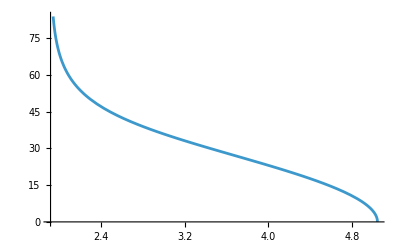

```mathematica
Plot[corrFEHom[ "trg"][r],{r,r2geo,r1geo}]
```

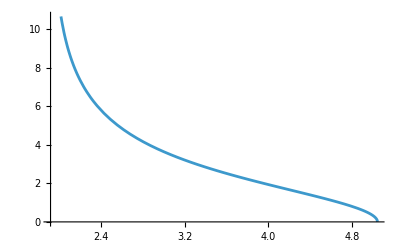

```mathematica
Plot[corrFEHom[ "ϕrg"][r],{r,r2geo,r1geo}]
```

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

Note: the correction to the radial motion, δr(r_g), is  defined at r_g=r_(2g) only if they are parametrized using the Mino-time λ.  δr(r_g) is not defined at when parametrized using the geodesic radial coordinate r_g. However,  δr(r_g) is finite in the limit r_g->r_(2g)

The correction to the radial motion is finite near the periastron

```mathematica
{corrFEHom["δrpar"][r2geo+10^-24],corrFEHom["δrpar"][r1geo]}
```

{-0.739926224437706908788810694317150725720064509414,-1.95071459169940912317050149714032552785163561469}

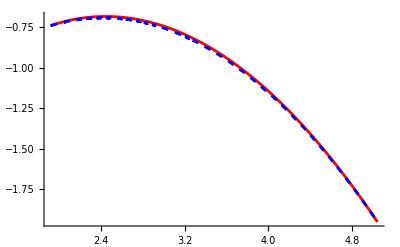

```mathematica
Show[Plot[corrFEHom["δrpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrFENearHom["δrOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the radial velocity

Note: the shift to the radial velocity, dδr/dλ, is defined at r_g=r_(2g) only if it is parametrized using the Mino-time λ. dδr/dλ is not defined at  r_g=r_(2g) when parametrized using the geodesic radial coordinate r_g. However, dδr/dλ is finite in the limit r_g->r_(2g)

```mathematica
{corrFEHom["δvrpar"][r2geo+10^-16],corrFEHom["δvrpar"][r1geo-10^-16]}
```

{5.85148675934186621×10^-17,-2.254228144399612386×10^-8}

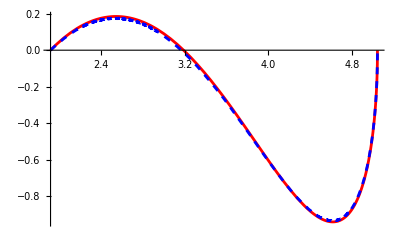

```mathematica
Show[Plot[corrFEHom["δvrpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrFENearHom["δvrOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the coordinate time and azimuthal trajectories

The shifts to the coordinate time and azimuthal trajectories diverge logarithmically at the periastron, as the corresponding geodesic trajectories

```mathematica
{corrFEHom["δtpar"][r2geo],corrFEHom["δtpar"][r1geo-10^(-14)]}
```

Power::infy: Infinite expression 1/0. encountered.

{Indeterminate,-1.9937259677168616248119×10^-6}

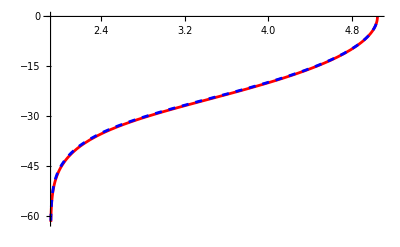

```mathematica
Show[Plot[corrFEHom["δtpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrFENearHom["δtOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

```mathematica
{corrFEHom["δϕpar"][r2geo],corrFEHom["δϕpar"][r1geo-10^(-14)]}
```

Power::infy: Infinite expression 1/0. encountered.

{Indeterminate,-8.1235782915359081949806×10^-8}

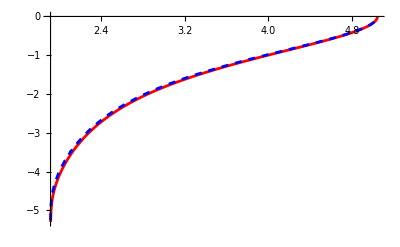

```mathematica
Show[Plot[corrFEHom["δϕpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrFENearHom["δϕOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the coordinate time and azimuthal velocities

Note: the shift to the coordinate time, dδt/dλ, and azimuthal velocities,dδϕ/dλ, are defined at r_g=r_(2g) only if they are parametrized using the Mino-time λ. dδt/dλ and dδϕ/dλ are not defined at when parametrized using the geodesic radial coordinate r_g. However, dδt/dλ and dδϕ/dλ are finite in the limit r_g->r_(2g)

The shift to the coordinate time velocity is finite near the periastron

```mathematica
{corrFEHom["δvtpar"][r2geo+10^-24],corrFEHom["δvtpar"][r1geo]}
```

{-0.7994515365160513135952149458395693091948645821,-23.1459768053019504242005653587446349333216422982}

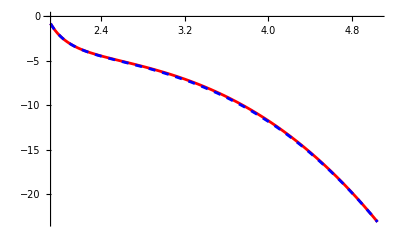

```mathematica
Show[Plot[corrFEHom["δvtpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrFENearHom["δvtOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

The shift to the azimuthal velocity is finite near the periastron

```mathematica
{corrFEHom["δvϕpar"][r2geo+10^-24],corrFEHom["δvϕpar"][r1geo]}
```

{0.95212207175046352005345076305023714850724660491,-0.609977167825303985946761289602423507786973367499}

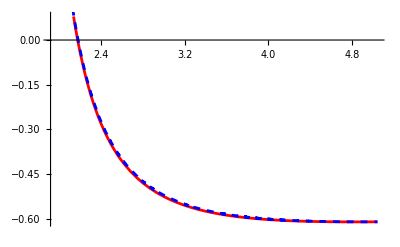

```mathematica
Show[Plot[corrFEHom["δvϕpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrFENearHom["δvϕOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrFEHom["MinoPrecessionFrequency"]
```

1.38323248705803294594290791977524474774356884387

Precession phase. It diverges logarithmically at the periastron

```mathematica
{corrFEHom["ψp"][r2geo],corrFEHom["ψp"][r1geo]}
```

{Indeterminate,0.}

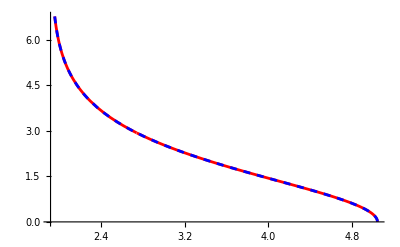

```mathematica
Show[Plot[corrFEHom["ψp"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrFENearHom["ψpOfr"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

Spin correction to the polar motion

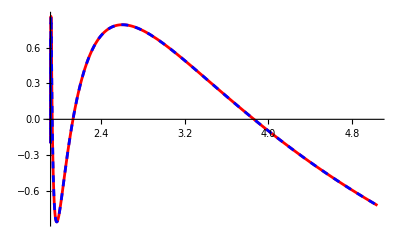

```mathematica
Show[Plot[corrFEHom["δzort"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrFENearHom["δzOfrort"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

## Plots orbits - fixed eccentricity

For plots

```mathematica
Integerise[num_]:=If[Round[num]==num,ToString[Round@num]<>".0",ToString@num]
```

#### Shifts separatrix

```mathematica
xbsep=Join[Table[{0.05i,,{0.015,0}},{i,0,100}],Table[{0.2i,Integerise[0.2i],{0.03,0}},{i,0,50}]];
```

```mathematica
xlsepFixecc=Join[Table[{0.1i,,{0.015,0}},{i,0,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,0,50}]];
xlsepFixspins=Join[Table[{0.01i,,{0.015,0}},{i,0,200}],Table[{0.05i,Integerise[0.05i],{0.03,0}},{i,0,50}]];
```

```mathematica
(*listprimaryspin={0,0.1,0.3,0.5,0.7,0.9,0.99`65,0.9999999999999`65};*)
listprimaryspin=Join[Table[i,{i,0,0.9,0.1}],{0.95,0.99,0.999,1`65-10^(-10)}];
(*listecc={0,0.1,0.3,0.5,0.7,0.9,0.99999999999`65};*)
listecc=Join[Table[i,{i,0,0.9,0.1}],{1`65-10^(-10)}];
```

```mathematica
psepgeofixeccpro=Table[KerrGeoSeparatrix[listprimaryspin[[i]],0.7`65,1],{i,Length[listprimaryspin]}];
psepgeofixspinspro=Table[KerrGeoSeparatrix[0.9`65,listecc[[i]],1],{i,Length[listecc]}];
```

```mathematica
psepgeofixeccret=Table[KerrGeoSeparatrix[listprimaryspin[[i]],0.7`65,-1],{i,Length[listprimaryspin]}];
psepgeofixspinsret=Table[KerrGeoSeparatrix[0.9`65,listecc[[i]],-1],{i,Length[listecc]}];
```

```mathematica
δpsepfixeccpro=Table[KerrNearEqSpinOrbitCorrFEHom[listprimaryspin[[i]],psepgeofixeccpro[[i]],0.7`65,1]["δp"],{i,Length[listprimaryspin]}];
δpsepfixspinspro=Table[KerrNearEqSpinOrbitCorrFEHom[0.9`65,psepgeofixspinspro[[i]],listecc[[i]],1]["δp"],{i,Length[listecc]}]//Quiet;
```

```mathematica
δpsepfixeccret=Table[KerrNearEqSpinOrbitCorrFEHom[listprimaryspin[[i]],psepgeofixeccret[[i]],0.7`65,-1]["δp"],{i,Length[listprimaryspin]}];
δpsepfixspinsret=Table[KerrNearEqSpinOrbitCorrFEHom[0.9`65,psepgeofixspinsret[[i]],listecc[[i]],-1]["δp"],{i,Length[listecc]}]//Quiet;
```

```mathematica
plotδpFixecc=ListPlot[Table[{listprimaryspin[[i]],-δpsepfixeccpro[[i]]},{i,Length[listprimaryspin]}],Frame->{{True,False},{True,False}},Joined->True,InterpolationOrder->3,PlotStyle->{Green},FrameLabel->{Style["a",Black],Style["-δp^*",Black]},FrameTicks->{{xlsepFixecc,None},{xbsep,None}},LabelStyle->{FontSize->15,FontFamily->"Times",Black},PlotLegends->Placed[{Style["e_g=0.7",15,Italic,FontFamily->"Times"]},Scaled[{0.20,0.25}]],PlotRange->{{0,1.025},{0,2.1}}];
```

```mathematica
plotδptFixspins=ListPlot[Table[{listecc[[i]],-δpsepfixspinspro[[i]]},{i,Length[listecc]}],Frame->{{True,False},{True,False}},Joined->True,InterpolationOrder->3,PlotStyle->{Blue},FrameLabel->{Style["e_g",Black],Style["-δp^*",Black]},FrameTicks->{{xlsepFixspins,None},{xbsep,None}},LabelStyle->{FontSize->15,FontFamily->"Times",Black},PlotLegends->Placed[{Style["a=0.9",15,Italic,FontFamily->"Times"]},Scaled[{0.20,0.25}]],PlotRange->{{0,1.025},All}];
```

```mathematica
(*separatrixplots=GraphicsRow[{plotδpFixecc,plotδptFixspins},Spacings->10,ImageSize->700,ImagePadding->{{-80, -20}, {-10, -10}}]*)
```

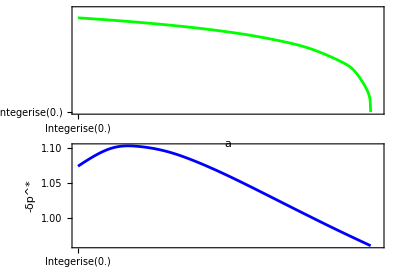

```mathematica
separatrixplots=GraphicsColumn[{plotδpFixecc,plotδptFixspins},Spacings->1,ImageSize->400]
```

```mathematica
(*Export["separatrix_plots.pdf",separatrixplots]*)
```

#### Spin correction periodic orbit - equatorial plane

```mathematica
xbperorb=Join[Table[{1i,,{0.015,0}},{i,0,100}],Table[{5i,Integerise[5i],{0.03,0}},{i,0,50}]];
xlδrperorb=Join[Table[{0.1i,,{0.015,0}},{i,-100,0}],Table[{0.5i,Integerise[i],{0.03,0}},{i,-50,0}]];
xlδtperorb=Join[Table[{2.5i,,{0.015,0}},{i,-100,100}],Table[{10i,Integerise[10i],{0.03,0}},{i,-50,50}]];
xlδϕperorb=Join[Table[{0.05i,,{0.015,0}},{i,-100,100}],Table[{0.25i,Integerise[0.25i],{0.03,0}},{i,-50,50}]];
```

```mathematica
KerrGeoSeparatrix[0.9,0.7,1]
```

3.07821

```mathematica
aPer=0.9;
eccPer=0.7;
pPer=KerrGeoSeparatrix[aPer,eccPer,1]+1/10;
```

```mathematica
AbsoluteTiming[corrFE=KerrNearEqSpinOrbitCorrFEPer[aPer,pPer,eccPer,1];]
```

{0.006931,Null}

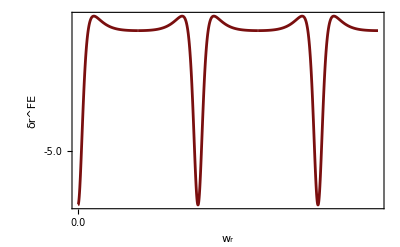

```mathematica
plotδrFE=Plot[corrFE["δrpar"][wr],{wr,0,5π},PlotStyle->DarkRed,Frame->{{True,False},{True,False}},FrameLabel->{Style["w_r",Black,21],Style["δr^FE",Black,21]},FrameTicks->{{xlδrperorb,None},{xbperorb,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,5π},All},ImageMargins->10,ImagePadding->{{75, 10}, {Automatic, 10}}]
```

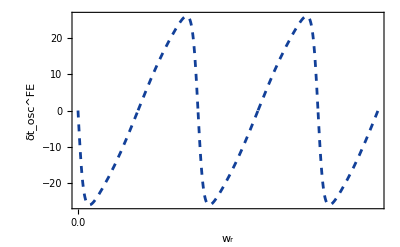

```mathematica
plotδtFE=Plot[corrFE["Δδtpar"][wr],{wr,0,5π},PlotStyle->{DarkBlue,Dashed},Frame->{{True,False},{True,False}},FrameLabel->{Style["w_r",Black,21],Style["δt_osc^FE",Black,21]},FrameTicks->{{xlδtperorb,True},{xbperorb,True}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,5π},All},Axes->False,ImageMargins->10,ImagePadding->{{75, 10}, {Automatic, 10}}]
```

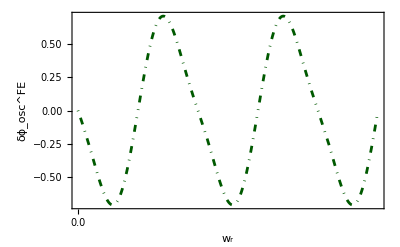

```mathematica
plotδϕFE=Plot[corrFE["Δδϕpar"][wr],{wr,0,5π},PlotStyle->{DarkGreen,DotDashed},Frame->{{True,False},{True,False}},FrameLabel->{Style["w_r",Black,21],Style["δϕ_osc^FE",Black,21]},FrameTicks->{{xlδϕperorb,True},{xbperorb,True}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,5π},All},Axes->False,ImageMargins->10,ImagePadding->{{75, 10}, {Automatic, 10}}]
```

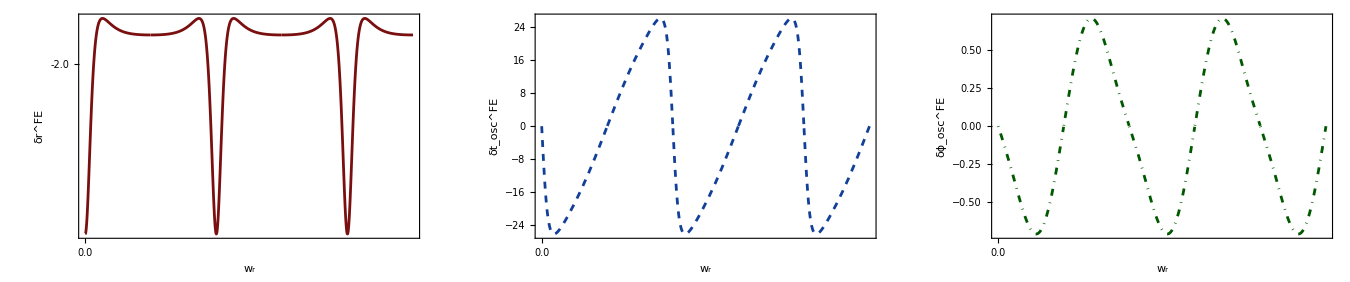

```mathematica
shiftperiodicorbitsplots=GraphicsRow[{plotδrFE,plotδtFE,plotδϕFE},Spacings->16,ImageSize->1350]
```

```mathematica
(*Export["shift_periodic_orbit_plots.pdf",shiftperiodicorbitsplots]*)
```

#### Spin correction homoclinic orbit - equatorial plane

```mathematica
xbhomorb=Join[Table[{0.05i,,{0.015,0}},{i,0,100}],Table[{0.2i,Integerise[0.2i],{0.03,0}},{i,0,50}]];
xlδrhomorb=Join[Table[{0.02i,,{0.015,0}},{i,0,100}],Table[{0.1i,Integerise[0.1i],{0.03,0}},{i,0,50}]];
xlδthomorb=Join[Table[{2.5i,,{0.015,0}},{i,-100,100}],Table[{10i,Integerise[10i],{0.03,0}},{i,-50,50}]];
xlδϕhomorb=Join[Table[{0.25i,,{0.015,0}},{i,-100,100}],Table[{1i,Integerise[i],{0.03,0}},{i,-50,50}]];
```

```mathematica
aHom=0.9;
eccHom=0.25;
```

```mathematica
psepgeo=KerrGeoSeparatrix[aHom,eccHom,1]
```

2.55205

```mathematica
r1geo=psepgeo/(1-eccHom);
r2geo=psepgeo/(1+eccHom);
```

```mathematica
AbsoluteTiming[corrFEHom=KerrNearEqSpinOrbitCorrFEHom[aHom,psepgeo,eccHom,1];]
```

{0.0052,Null}

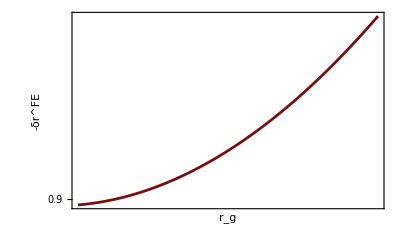

```mathematica
plotδrFEHom=Plot[-corrFEHom["δrpar"][r],{r,r2geo,r1geo},PlotStyle->DarkRed,Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["-δr^FE",Black,21]},FrameTicks->{{xlδrhomorb,True},{xbhomorb,True}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{r2geo,r1geo},All},ImageMargins->10,ImagePadding->{{75, 10}, {Automatic, 10}}]
```

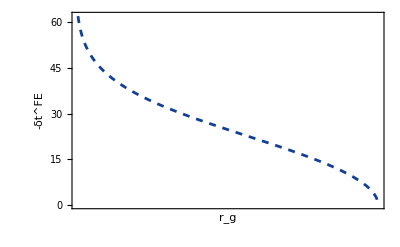

```mathematica
plotδtFEHom=Plot[-corrFEHom["δtpar"][r],{r,r2geo+ 2 10^(-3),r1geo},PlotStyle->{DarkBlue,Dashed},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["-δt^FE",Black,21]},FrameTicks->{{xlδthomorb,True},{xbhomorb,True}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{r2geo,r1geo},{62,0}},Axes->False,ImageMargins->10,ImagePadding->{{75, 10}, {Automatic, 10}}]
```

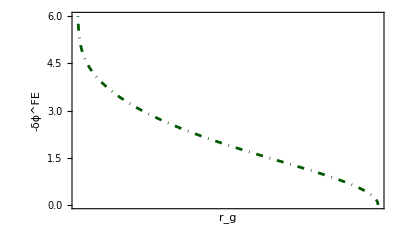

```mathematica
plotδϕFEHom=Plot[-corrFEHom["δϕpar"][r],{r,r2geo+ 5 10^(-4),r1geo},PlotStyle->{DarkGreen,DotDashed},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["-δϕ^FE",Black,21]},FrameTicks->{{xlδϕhomorb,True},{xbhomorb,True}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{r2geo,r1geo},{6,0}},Axes->False,ImageMargins->10,ImagePadding->{{75, 10}, {Automatic, 10}}]
```

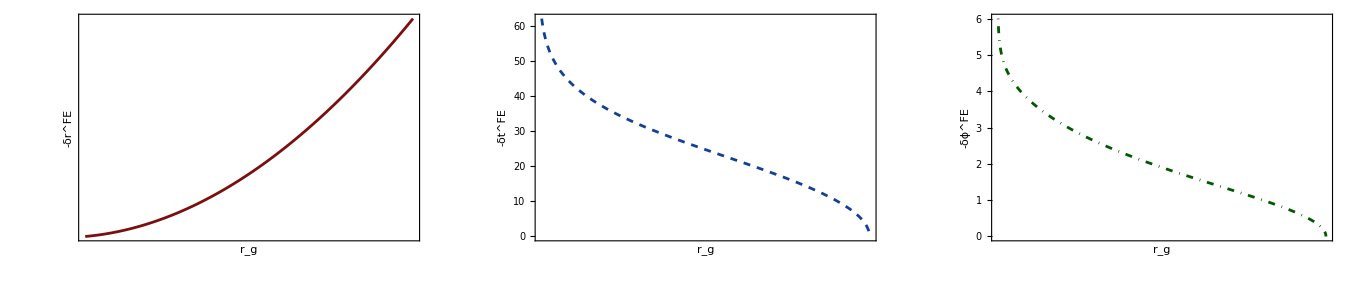

```mathematica
shifthomoclinicorbitsplots=GraphicsRow[{plotδrFEHom,plotδtFEHom,plotδϕFEHom},Spacings->16,ImageSize->1350]
```

```mathematica
(*Export["shift_homoclinic_orbit_plots.pdf",shifthomoclinicorbitsplots]*)
```

#### Showcase periodic orbits

```mathematica
xperorbshowcase=Join[Table[{0.5i,,{0.015,0}},{i,-100,100}],Table[{2.5i,Integerise[2.5i],{0.03,0}},{i,-50,50}]];
yperorbshowcase=Join[Table[{0.005i,,{0.015,0}},{i,-100,100}],Table[{0.02i,Integerise[0.02i],{0.03,0}},{i,-50,50}]];
```

```mathematica
KerrGeoSeparatrix[0.9,0.7,1]
```

3.07821

```mathematica
aPer=0.9;
eccPer=0.7;
pPer=KerrGeoSeparatrix[aPer,eccPer,1]+1/10;
```

```mathematica
r1gPer=pPer/(1-eccPer);
r2gPer=pPer/(1+eccPer);
```

```mathematica
AbsoluteTiming[corrFE=KerrNearEqSpinOrbitCorrFEPerFourier[aPer,pPer,eccPer,1,12];]
```

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.130447,Null}

```mathematica
{Υtg,Υrg,Υzg,Υϕg}=corrFE["MinoFrequenciesGeo"]
```

{30.0645,0.881363,2.42084,3.6096}

```mathematica
{δΥt,δΥr,δΥϕ}=corrFE["MinoFrequenciesCorrection"]
```

{-8.76062,0.192631,-0.0816186}

```mathematica
rg[wr_]:=corrFE["rg"][wr];
δrpar[wr_]:=corrFE["δrpar"][wr];
```

```mathematica
ϕg[wr_]:=1/Υrg Υϕg wr+corrFE["Δϕrg"][wr];
δϕpar[wr_]:=1/Υrg(δΥϕ-Υϕg/Υrg δΥr)wr+corrFE["Δδϕpar"][wr];
```

```mathematica
δzort[wr_]:=corrFE["δzort"][wr];
```

```mathematica
χpar=1/2;
(*q=1/25;*)
(*q=1/20;*)
q=1/100;
```

```mathematica
σpar=q*χpar;
σort=q*√(1-χpar^2);
```

```mathematica
Equatorr1g=Table[{r1gPer*Sin[π/2]Cos[n],r1gPer*Sin[π/2]Sin[n],r1gPer*Cos[π/2]},{n,0,2π,0.001}];
Equatorr2g=Table[{r2gPer*Sin[π/2]Cos[n],r2gPer*Sin[π/2]Sin[n],r2gPer*Cos[π/2]},{n,0,2π,0.001}];
```

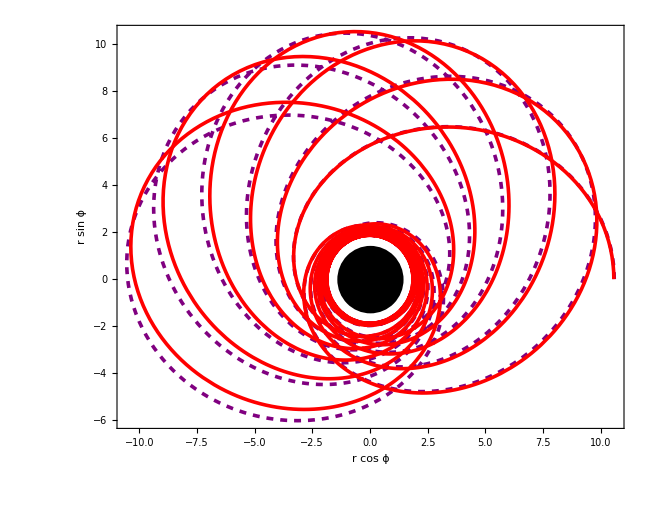

```mathematica
BirdsEyePer=Show[ParametricPlot[{rg[wr] Cos[ϕg[wr]],rg[wr]Sin[ϕg[wr]]},{wr,0,11π},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xperorbshowcase,True},{xperorbshowcase,True}}],ParametricPlot[{(rg[wr]+σpar δrpar[wr]) Cos[ϕg[wr]+σpar δϕpar[wr]],(rg[wr]+σpar δrpar[wr])Sin[ϕg[wr]+σpar δϕpar[wr]]},{wr,0,11π},PlotStyle->{Thickness[0.004],Red},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xperorbshowcase,True},{xperorbshowcase,True}}],Graphics[{Black,Disk[{0,0},1+√(1-aPer^2)]}],ImageSize->650]
```

```mathematica
(*Export["zoom_whirl_orbit_birds_eye.pdf",BirdsEyePer]*)
```

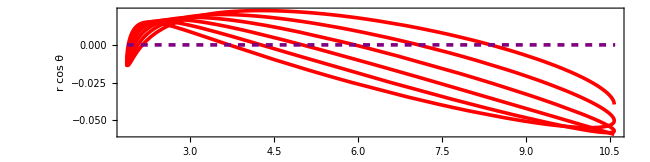

```mathematica
MeridionalPer=Show[ParametricPlot[{(rg[wr]+σpar δrpar[wr]) Sin[π/2-σort δzort[wr]],(rg[wr]+σpar δrpar[wr])Cos[π/2-σort δzort[wr]]},{wr,0,6π},Method->{"ShrinkWrap"->True},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r sin θ",18],Style["r cos θ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},AspectRatio->1/4,FrameTicks->{{yperorbshowcase,True},{xperorbshowcase,True}}],Graphics[{Purple,Thickness[0.004],Dashed,Line[{{r2gPer,0},{r1gPer,0}}]}],ImageSize->650]
```

```mathematica
(*Export["zoom_whirl_orbit_meridional.pdf",MeridionalPer]*)
```

```mathematica
(*GenericViewPer =  Show[ParametricPlot3D[({rg[wr] Cos[ϕg[wr]]Sin[π/2],rg[wr]Sin[ϕg[wr]]Sin[π/2],rg[wr]Cos[π/2]}),{wr,0,12π},PlotStyle->{Purple,Dashed},Axes->False,Boxed->False,Axes->False,Lighting->"ThreePoint",PlotStyle->Purple,PlotRange->All],ParametricPlot3D[({(rg[wr]+σpar δrpar[wr]) Cos[ϕg[wr]+σpar δϕpar[wr]]Sin[π/2-σort δzort[wr]],(rg[wr]+σpar δrpar[wr])Sin[ϕg[wr]+σpar δϕpar[wr]]Sin[π/2-σort δzort[wr]],(rg[wr]+σpar δrpar[wr])Cos[π/2-σort δzort[wr]]}),{wr,0,12π},PlotStyle->Red,Boxed->False,Axes->False,Lighting->"ThreePoint",MaxRecursion->10,PlotPoints->4000,PlotStyle->Purple,Method->{"ShrinkWrap"->True},PlotRange->All,Exclusions->None],Graphics3D[{MaterialShading[<|"BaseColor"->GrayLevel[0.4],"MetallicCoefficient"->1,"RoughnessCoefficient"->0.65|>],Sphere[{0,0,0},N[1+Sqrt[1-aPer^2]]]}]]*)
```

#### Showcase homoclinic orbits

```mathematica
xhomorbshowcase=Join[Table[{0.5i,,{0.015,0}},{i,-100,100}],Table[{2.5i,Integerise[2.5i],{0.03,0}},{i,-50,50}]];
yhomorbshowcase=Join[Table[{0.05i,,{0.015,0}},{i,-100,100}],Table[{0.1i,Integerise[0.1i],{0.03,0}},{i,-50,50}]];
```

```mathematica
aHom=0.9;
eccHom=0.5;
```

```mathematica
psepgeo=KerrGeoSeparatrix[aHom,eccHom,1]
```

2.83324

```mathematica
r1gHom=psepgeo/(1-eccHom)
r2gHom=psepgeo/(1+eccHom)
```

5.66647

1.88882

```mathematica
AbsoluteTiming[corrFEHom=KerrNearEqSpinOrbitCorrFEHom[aHom,psepgeo,eccHom,1];]
```

{0.016104,Null}

```mathematica
rgHom[λ_]:=corrFEHom["rg"][λ];
δrparHom[λ_]:=corrFEHom["δrpar"][rgHom[λ]];
```

```mathematica
ϕgHom[λ_]:=corrFEHom["ϕrg"][rgHom[λ]];
δϕparHom[λ_]:=corrFEHom["δϕpar"][rgHom[λ]];
```

```mathematica
δzortHom[λ_]:=corrFEHom["δzort"][rgHom[λ]];
```

```mathematica
χpar=1/2;
(*q=1/25;*)
q=1/10;
```

```mathematica
σpar=q*χpar;
σort=q*√(1-χpar^2);
```

```mathematica
√(1-χpar^2)//N
```

0.866025

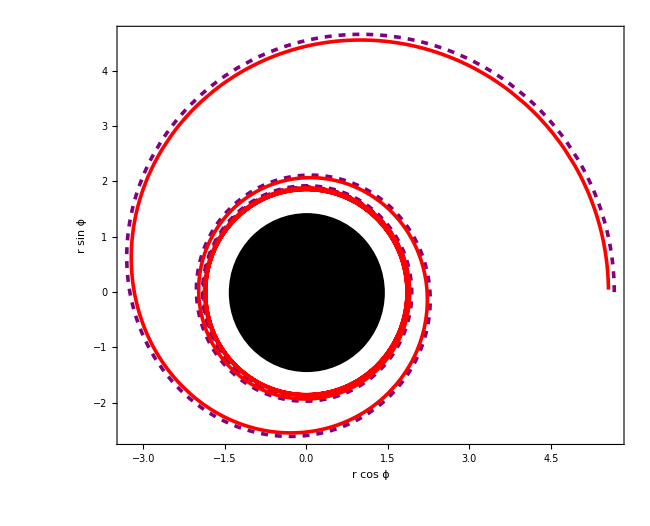

```mathematica
BirdsEyeHom = Show[ParametricPlot[({(rgHom[λ])Cos[ϕgHom[λ]],(rgHom[λ])Sin[ϕgHom[λ]]}),{λ,10^(-9),10},PlotRange->All,PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xhomorbshowcase,True},{xhomorbshowcase,True}}],ParametricPlot[({(rgHom[λ]+σpar δrparHom[λ]) Cos[ϕgHom[λ]+σpar δϕparHom[λ]],(rgHom[λ]+σpar δrparHom[λ])Sin[ϕgHom[λ]+σpar δϕparHom[λ]]}),{λ,10^(-9),10},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xhomorbshowcase,True},{xhomorbshowcase,True}}],Graphics[{Black,Disk[{0,0},1+√(1-aHom^2)]}],ImageSize->650]
```

```mathematica
(*Export["homoclinic_birds_eye.pdf",BirdsEyeHom]*)
```

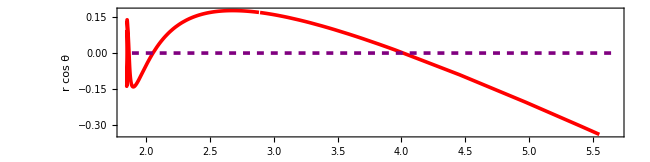

```mathematica
MeridionalHom = Show[ParametricPlot[{(rgHom[r]+σpar δrparHom[r]) Sin[π/2-σort δzortHom[r]],(rgHom[r]+σpar δrparHom[r])Cos[π/2-σort δzortHom[r]]},{r,0,10},PlotRange->All,PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r sin θ",18],Style["r cos θ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},AspectRatio->1/4],Graphics[{Purple,Thickness[0.004],Dashed,Line[{{r2gHom,0},{r1gHom,0}}]}],ImageSize->650,FrameTicks->{{yhomorbshowcase,True},{xhomorbshowcase,True}}]
```

```mathematica
(*Export["homoclinic_meridional.pdf",MeridionalHom]*)
```

```mathematica
(*GenericViewHom =  Show[ParametricPlot3D[{rgHom[λ] Cos[ϕgHom[λ]]Sin[π/2],rgHom[λ]Sin[ϕgHom[λ]]Sin[π/2],rgHom[λ]Cos[π/2]},{λ,0,10},PlotStyle->{Purple,Dashed},Axes->False,Boxed->False,Axes->False,Lighting->"ThreePoint",Method->{"ShrinkWrap"->True},PlotRange->All],ParametricPlot3D[({(rgHom[λ]+σpar δrparHom[λ]) Cos[ϕgHom[λ]+σpar δϕparHom[λ]]Sin[π/2-σort δzortHom[λ]],(rgHom[λ]+σpar δrparHom[λ])Sin[ϕgHom[λ]+σpar δϕparHom[λ]]Sin[π/2-σort δzortHom[λ]],(rgHom[λ]+σpar δrparHom[λ])Cos[π/2-σort δzortHom[λ]]}),{λ,0,10},PlotStyle->{Red,Thick},Boxed->False,Axes->False,Lighting->"ThreePoint",MaxRecursion->10,PlotPoints->500,Method->{"ShrinkWrap"->True},PlotRange->All],Graphics3D[{MaterialShading[<|"BaseColor"->GrayLevel[0.4],"MetallicCoefficient"->1,"RoughnessCoefficient"->0.65|>],Sphere[{0,0,0},N[1+Sqrt[1-aHom^2]]]}]]
*)
```